```mathematica
Hz[x_,z_]:=((8 mr)/π^2 )*Sum[((1/n)*Sin[(n*Pi*x)/a]*(1-Exp[-Pi*(n/a)*δ])*Exp[-Pi*(n/a)*z]),{n,1,50,2}];
```

```mathematica
Hx[x_,z_]:=((-8 mr)/π^2 )*Sum[((1/n)*Cos[(n*Pi*x)/a]*(1-Exp[-Pi*(n/a)*δ])*Exp[-Pi*(n/a)*z]),{n,1,50,2}];
```

```mathematica
HGzz[x_,z_]:=Evaluate[D[Hz[x,z],z]];
HGzx[x_,z_]:=Evaluate[D[Hz[x,z],x]];
HGxz[x_,z_]:=Evaluate[D[Hx[x,z],z]];
HGxx[x_,z_]:=Evaluate[D[Hx[x,z],x]];
```

```mathematica
ff[Ha_,Ms_]:=If[Ha<Ms/3,3,Ms/Ha];
```

```mathematica
Vp[r_]:=4 Pi r^3/3;   (*NP radius r; in nm*)
Fmx[x_,z_,Rp_,Ms_]:=mu0 Vp[Rp] ff[Sqrt[Hx[x,z]^2+Hz[x,z]^2],Ms] (Hx[x,z] HGxx[x,z]+Hz[x,z] HGxz[x,z]); (*Furlani_JAP_2006 eqn 15;Force units are cancelled with mass m*)
Fmz[x_,z_,Rp_,Ms_]:=mu0 Vp[Rp] ff[Sqrt[Hx[x,z]^2+Hz[x,z]^2],Ms](Hx[x,z] HGzx[x,z]+ Hz[x,z]HGzz[x,z]);(*Furlani_JAP_2006 eqn 15;Force units are cancelled with mass m*)
```

```mathematica
Hz[x,z]
```

1/π^2 8 mr (ⅇ^(-(π z)/a) (1-ⅇ^(-(π δ)/a)) Sin[(π x)/a]+1/3 ⅇ^(-(3 π z)/a) (1-ⅇ^(-(3 π δ)/a)) Sin[(3 π x)/a]+1/5 ⅇ^(-(5 π z)/a) (1-ⅇ^(-(5 π δ)/a)) Sin[(5 π x)/a]+1/7 ⅇ^(-(7 π z)/a) (1-ⅇ^(-(7 π δ)/a)) Sin[(7 π x)/a]+1/9 ⅇ^(-(9 π z)/a) (1-ⅇ^(-(9 π δ)/a)) Sin[(9 π x)/a]+1/11 ⅇ^(-(11 π z)/a) (1-ⅇ^(-(11 π δ)/a)) Sin[(11 π x)/a]+1/13 ⅇ^(-(13 π z)/a) (1-ⅇ^(-(13 π δ)/a)) Sin[(13 π x)/a]+1/15 ⅇ^(-(15 π z)/a) (1-ⅇ^(-(15 π δ)/a)) Sin[(15 π x)/a]+1/17 ⅇ^(-(17 π z)/a) (1-ⅇ^(-(17 π δ)/a)) Sin[(17 π x)/a]+1/19 ⅇ^(-(19 π z)/a) (1-ⅇ^(-(19 π δ)/a)) Sin[(19 π x)/a]+1/21 ⅇ^(-(21 π z)/a) (1-ⅇ^(-(21 π δ)/a)) Sin[(21 π x)/a]+1/23 ⅇ^(-(23 π z)/a) (1-ⅇ^(-(23 π δ)/a)) Sin[(23 π x)/a]+1/25 ⅇ^(-(25 π z)/a) (1-ⅇ^(-(25 π δ)/a)) Sin[(25 π x)/a]+1/27 ⅇ^(-(27 π z)/a) (1-ⅇ^(-(27 π δ)/a)) Sin[(27 π x)/a]+1/29 ⅇ^(-(29 π z)/a) (1-ⅇ^(-(29 π δ)/a)) Sin[(29 π x)/a]+1/31 ⅇ^(-(31 π z)/a) (1-ⅇ^(-(31 π δ)/a)) Sin[(31 π x)/a]+1/33 ⅇ^(-(33 π z)/a) (1-ⅇ^(-(33 π δ)/a)) Sin[(33 π x)/a]+1/35 ⅇ^(-(35 π z)/a) (1-ⅇ^(-(35 π δ)/a)) Sin[(35 π x)/a]+1/37 ⅇ^(-(37 π z)/a) (1-ⅇ^(-(37 π δ)/a)) Sin[(37 π x)/a]+1/39 ⅇ^(-(39 π z)/a) (1-ⅇ^(-(39 π δ)/a)) Sin[(39 π x)/a]+1/41 ⅇ^(-(41 π z)/a) (1-ⅇ^(-(41 π δ)/a)) Sin[(41 π x)/a]+1/43 ⅇ^(-(43 π z)/a) (1-ⅇ^(-(43 π δ)/a)) Sin[(43 π x)/a]+1/45 ⅇ^(-(45 π z)/a) (1-ⅇ^(-(45 π δ)/a)) Sin[(45 π x)/a]+1/47 ⅇ^(-(47 π z)/a) (1-ⅇ^(-(47 π δ)/a)) Sin[(47 π x)/a]+1/49 ⅇ^(-(49 π z)/a) (1-ⅇ^(-(49 π δ)/a)) Sin[(49 π x)/a])

```mathematica
Manipulate[Plot[((8 mr)/π^2 )*Sum[((1/n)*Sin[(n*Pi*x)/a]*(1-Exp[-Pi*(n/a)*δ])*Exp[-Pi*(n/a)*z]),{n,1,50,2}],{x,-1000,1000 },PlotRange->{{x1,x2},{y1,y2}},Frame->True,FrameLabel->{"In-plane distance (nm)","Magnetic Field (Tesla)"},PlotStyle->{{Thickness->0.01}},GridLines->None,FrameStyle->{{Directive[Thick,FontFamily->"Arial",Black,18],Directive[Thick,FontFamily->"Arial",Black,18]},{Directive[Thick,FontFamily->"Arial",Black,18],Directive[Thick,FontFamily->"Arial",Black,18]}}],{z,.1,750},{mr,1,1000 10^3},{a,10,1000 },{δ,1 ,100},{x1,-1,0},{x2,0,1000 },{y1,-100,0},{y2,0,100}]
```

```mathematica
Manipulate[Plot[1/π^2 8 mr (ⅇ^(-(π z)/a) (1-ⅇ^(-(π δ)/a)) Sin[(π x)/a]+1/3 ⅇ^(-(3 π z)/a) (1-ⅇ^(-(3 π δ)/a)) Sin[(3 π x)/a]+1/5 ⅇ^(-(5 π z)/a) (1-ⅇ^(-(5 π δ)/a)) Sin[(5 π x)/a]+1/7 ⅇ^(-(7 π z)/a) (1-ⅇ^(-(7 π δ)/a)) Sin[(7 π x)/a]+1/9 ⅇ^(-(9 π z)/a) (1-ⅇ^(-(9 π δ)/a)) Sin[(9 π x)/a]+1/11 ⅇ^(-(11 π z)/a) (1-ⅇ^(-(11 π δ)/a)) Sin[(11 π x)/a]+1/13 ⅇ^(-(13 π z)/a) (1-ⅇ^(-(13 π δ)/a)) Sin[(13 π x)/a]+1/15 ⅇ^(-(15 π z)/a) (1-ⅇ^(-(15 π δ)/a)) Sin[(15 π x)/a]+1/17 ⅇ^(-(17 π z)/a) (1-ⅇ^(-(17 π δ)/a)) Sin[(17 π x)/a]+1/19 ⅇ^(-(19 π z)/a) (1-ⅇ^(-(19 π δ)/a)) Sin[(19 π x)/a]+1/21 ⅇ^(-(21 π z)/a) (1-ⅇ^(-(21 π δ)/a)) Sin[(21 π x)/a]+1/23 ⅇ^(-(23 π z)/a) (1-ⅇ^(-(23 π δ)/a)) Sin[(23 π x)/a]+1/25 ⅇ^(-(25 π z)/a) (1-ⅇ^(-(25 π δ)/a)) Sin[(25 π x)/a]+1/27 ⅇ^(-(27 π z)/a) (1-ⅇ^(-(27 π δ)/a)) Sin[(27 π x)/a]+1/29 ⅇ^(-(29 π z)/a) (1-ⅇ^(-(29 π δ)/a)) Sin[(29 π x)/a]+1/31 ⅇ^(-(31 π z)/a) (1-ⅇ^(-(31 π δ)/a)) Sin[(31 π x)/a]+1/33 ⅇ^(-(33 π z)/a) (1-ⅇ^(-(33 π δ)/a)) Sin[(33 π x)/a]+1/35 ⅇ^(-(35 π z)/a) (1-ⅇ^(-(35 π δ)/a)) Sin[(35 π x)/a]+1/37 ⅇ^(-(37 π z)/a) (1-ⅇ^(-(37 π δ)/a)) Sin[(37 π x)/a]+1/39 ⅇ^(-(39 π z)/a) (1-ⅇ^(-(39 π δ)/a)) Sin[(39 π x)/a]+1/41 ⅇ^(-(41 π z)/a) (1-ⅇ^(-(41 π δ)/a)) Sin[(41 π x)/a]+1/43 ⅇ^(-(43 π z)/a) (1-ⅇ^(-(43 π δ)/a)) Sin[(43 π x)/a]+1/45 ⅇ^(-(45 π z)/a) (1-ⅇ^(-(45 π δ)/a)) Sin[(45 π x)/a]+1/47 ⅇ^(-(47 π z)/a) (1-ⅇ^(-(47 π δ)/a)) Sin[(47 π x)/a]+1/49 ⅇ^(-(49 π z)/a) (1-ⅇ^(-(49 π δ)/a)) Sin[(49 π x)/a]),{x,-1000,1000 },PlotRange->{{x1,x2},{y1,y2}},Frame->True,FrameLabel->{"In-plane distance (nm)","Magnetic Field (Tesla)"},PlotStyle->{{Thickness->0.01}},GridLines->None,FrameStyle->{{Directive[Thick,FontFamily->"Arial",Black,18],Directive[Thick,FontFamily->"Arial",Black,18]},{Directive[Thick,FontFamily->"Arial",Black,18],Directive[Thick,FontFamily->"Arial",Black,18]}}],{z,.1,750},{mr,1,1000 10^3},{a,10,1000 },{δ,1 ,100},{x1,-1,0},{x2,0,1000 },{y1,-100,0},{y2,0,100}]
```

```mathematica
Manipulate[Plot[Hz[x_,z_],{x,-1000,1000 },PlotRange->{{x1,x2},{y1,y2}},Frame->True,FrameLabel->{"In-plane distance (nm)","Magnetic Field (Tesla)"},PlotStyle->{{Thickness->0.01}},GridLines->None,FrameStyle->{{Directive[Thick,FontFamily->"Arial",Black,18],Directive[Thick,FontFamily->"Arial",Black,18]},{Directive[Thick,FontFamily->"Arial",Black,18],Directive[Thick,FontFamily->"Arial",Black,18]}}],{z,.1,750},{mr,1,1000 10^3},{a,10,1000 },{δ,1 ,100},{x1,-1,0},{x2,0,1000 },{y1,-100,0},{y2,0,100}]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAll["Global"]
```

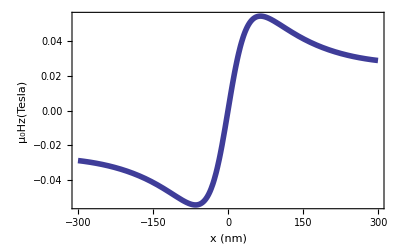

```mathematica
Plot[4 Pi 10^-7((8 450000)/π^2 )*Sum[((1/n)*Sin[(n*Pi*x)/750]*(1-Exp[-Pi*(n/750)*30])*Exp[-Pi*(n/750)*50]),{n,1,50,2}],{x,-300,300},PlotRange->All,Frame->True,FrameLabel->{"x (nm)","μ_0Hz(Tesla)"},PlotStyle->{{Thickness->0.01}},GridLines->None,FrameStyle->{{Directive[Thick,FontFamily->"Arial",Black,18],Directive[Thick,FontFamily->"Arial",Black,18]},{Directive[Thick,FontFamily->"Arial",Black,18],Directive[Thick,FontFamily->"Arial",Black,18]}}]
```

```mathematica
R1=((-8 mr)/π^2 )*Sum[((1/n)*Cos[(n*Pi*x)/a]*(1-Exp[-Pi*(n/a)*δ])*Exp[-Pi*(n/a)*z]),{n,1,50,2}];
```

```mathematica
Plot[4 Pi 10^-7 R1,{x,-300,300},PlotRange->All,Frame->True,FrameLabel->{"x (nm)","μ_0Hz(Tesla)"},PlotStyle->{{Thickness->0.01}},GridLines->None,FrameStyle->{{Directive[Thick,FontFamily->"Arial",Black,18],Directive[Thick,FontFamily->"Arial",Black,18]},{Directive[Thick,FontFamily->"Arial",Black,18],Directive[Thick,FontFamily->"Arial",Black,18]}}]
```

-Graphics-

```mathematica
Hx
```

Hx

```mathematica
Hx[x,z]
```

-1/π^2 8 mr (ⅇ^(-(π z)/a) (1-ⅇ^(-(π δ)/a)) Cos[(π x)/a]+1/3 ⅇ^(-(3 π z)/a) (1-ⅇ^(-(3 π δ)/a)) Cos[(3 π x)/a]+1/5 ⅇ^(-(5 π z)/a) (1-ⅇ^(-(5 π δ)/a)) Cos[(5 π x)/a]+1/7 ⅇ^(-(7 π z)/a) (1-ⅇ^(-(7 π δ)/a)) Cos[(7 π x)/a]+1/9 ⅇ^(-(9 π z)/a) (1-ⅇ^(-(9 π δ)/a)) Cos[(9 π x)/a]+1/11 ⅇ^(-(11 π z)/a) (1-ⅇ^(-(11 π δ)/a)) Cos[(11 π x)/a]+1/13 ⅇ^(-(13 π z)/a) (1-ⅇ^(-(13 π δ)/a)) Cos[(13 π x)/a]+1/15 ⅇ^(-(15 π z)/a) (1-ⅇ^(-(15 π δ)/a)) Cos[(15 π x)/a]+1/17 ⅇ^(-(17 π z)/a) (1-ⅇ^(-(17 π δ)/a)) Cos[(17 π x)/a]+1/19 ⅇ^(-(19 π z)/a) (1-ⅇ^(-(19 π δ)/a)) Cos[(19 π x)/a]+1/21 ⅇ^(-(21 π z)/a) (1-ⅇ^(-(21 π δ)/a)) Cos[(21 π x)/a]+1/23 ⅇ^(-(23 π z)/a) (1-ⅇ^(-(23 π δ)/a)) Cos[(23 π x)/a]+1/25 ⅇ^(-(25 π z)/a) (1-ⅇ^(-(25 π δ)/a)) Cos[(25 π x)/a]+1/27 ⅇ^(-(27 π z)/a) (1-ⅇ^(-(27 π δ)/a)) Cos[(27 π x)/a]+1/29 ⅇ^(-(29 π z)/a) (1-ⅇ^(-(29 π δ)/a)) Cos[(29 π x)/a]+1/31 ⅇ^(-(31 π z)/a) (1-ⅇ^(-(31 π δ)/a)) Cos[(31 π x)/a]+1/33 ⅇ^(-(33 π z)/a) (1-ⅇ^(-(33 π δ)/a)) Cos[(33 π x)/a]+1/35 ⅇ^(-(35 π z)/a) (1-ⅇ^(-(35 π δ)/a)) Cos[(35 π x)/a]+1/37 ⅇ^(-(37 π z)/a) (1-ⅇ^(-(37 π δ)/a)) Cos[(37 π x)/a]+1/39 ⅇ^(-(39 π z)/a) (1-ⅇ^(-(39 π δ)/a)) Cos[(39 π x)/a]+1/41 ⅇ^(-(41 π z)/a) (1-ⅇ^(-(41 π δ)/a)) Cos[(41 π x)/a]+1/43 ⅇ^(-(43 π z)/a) (1-ⅇ^(-(43 π δ)/a)) Cos[(43 π x)/a]+1/45 ⅇ^(-(45 π z)/a) (1-ⅇ^(-(45 π δ)/a)) Cos[(45 π x)/a]+1/47 ⅇ^(-(47 π z)/a) (1-ⅇ^(-(47 π δ)/a)) Cos[(47 π x)/a]+1/49 ⅇ^(-(49 π z)/a) (1-ⅇ^(-(49 π δ)/a)) Cos[(49 π x)/a])